```mathematica
NS[]
```

```mathematica
l=211;k=5695;
```

```mathematica
nx=k+1;kk=10000;
(Binomial[k,nx]/Binomial[kk,nx])//Log//N
```

-∞

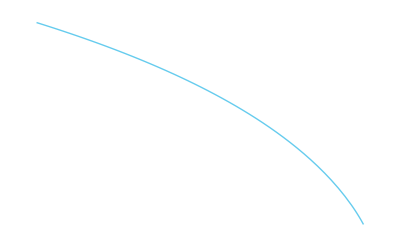

```mathematica
Plot[Log[Binomial[k,x]/Binomial[kk,x]],{x,0,k},PlotRange->{All,Auto}]
```

```mathematica
Plot3D[Log[Binomial[k,x]/Binomial[10^nkk,x]],{x,0,k},{nkk,Log[10,k],Log[10,k*10]},PlotRange->{All,All,Auto},Axes->True,AxesLabel->Auto]
```

-Graphics3D-

```mathematica
nx=k;kk=10000;
(Binomial[k,nx]/Binomial[kk,nx])//Log//N
```

-6829.73

```mathematica
Assuming[0<q<1,FS[Log[((1-q^l)^k)*(q^(l*kk))]]]
```

Log[q^2110000 (1-q^211)^5695]

```mathematica
(((1-(1-q)^l)^(1/l)*q)/.{q->1/2})//N
```

0.5

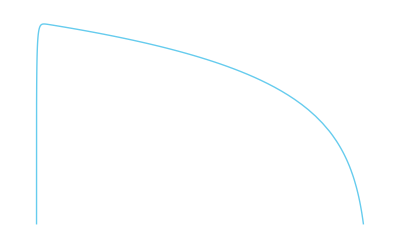

```mathematica
Plot[Log[(1-(1-q)^l)^(k/kk)*(1-q)],{q,0,1},PlotRange->{All,Auto}]
```

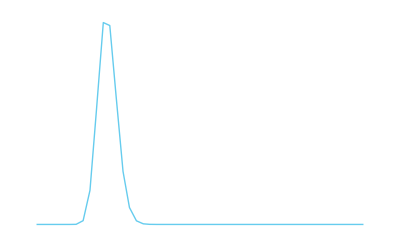

```mathematica
Plot[Evaluate@Table[((1-(1-q)^l)^(k/(l*kkx))*(1-q))^(l*100),{kkx,{10000}}],{q,0,0.01},PlotRange->{All,All}]
```

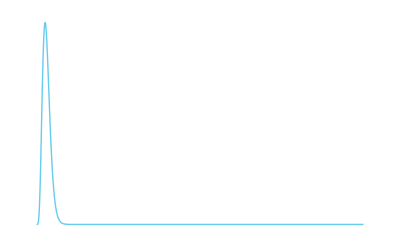

```mathematica
Plot[Evaluate@Table[((1-(1-q)^l)^(k/(l*kkx))*(1-q))^(l*100),{kkx,{100000}}],{q,0,0.01},PlotRange->{All,All}]
```

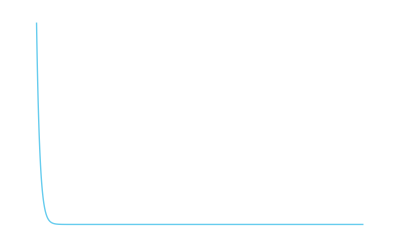

```mathematica
Plot[((1-(1-q)^l)^(1/kk)*(1-q))^100,{q,0,1},PlotRange->{All,Auto}]
```

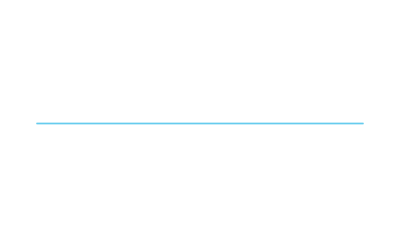

```mathematica
kk=10000;
Plot[Table[(1-q^l)^k*q^(l*kkx),{kkx,{10000,100000}}],{q,0,1},PlotRange->{All,Auto}]
```